# 快速Sqrt函数

如何求√4 的值？
分析 ：√4=x , x^2=4 , x^2-4=0 ,把函数图像画出后就是下图蓝色曲线，函数0点的x值就是所求
牛顿迭代法：先令x=4,过(4 ,f(4))做函数切线，x=4时抛物线上的切点是(4,12),斜率是2x=8,可以点斜式做出切线，求切线与x轴交点8(x-4)+12=0 ,x=2.5
		2.5就更加接近0点，令x=2.5重复上述步骤。

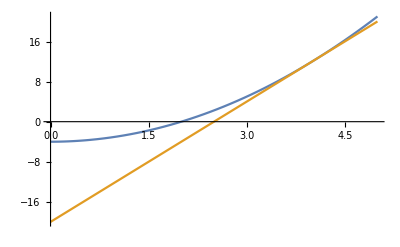

```mathematica
Plot[{x^2-4,8(x-4)+12},{x,0,5}]
```

更通用的做法：f(x)=x^2+a 假设切线与x轴交点是b
因为斜率就是f(x)/(x-b)=斜率=2x , f(x)/2x=x-b , b = x-f(x)/2x

```mathematica
(*牛顿法交互图形演示，NewtonInteractive接受两个参数，n是待开平方数，accuracy是精确度,返回Sqrt[N]的近似解*)
NewtonInteractive[n_,accuracy_]:=Module[{x=n},
	For[i=0,i<accuracy,i++,x=x-(x^2-n)/(2x)];
x
];
NewtonInteractive[2,5]//N[#,20]&
```

1.4142135623730950488

```mathematica
Manipulate[Column[{NewtonInteractive[a,accuracy],Plot[{x^2-a,2*NewtonInteractive[a,accuracy]*(x-NewtonInteractive[a,accuracy])+NewtonInteractive[a,accuracy]^2-a},{x,0,10}]}],{a,1,10},{accuracy,1,5,1}]
```